http://community.wolfram.com/groups/-/m/t/1226104

Copula models applied in pairs trading:

This datadrop is collecting 5-minute data in the form of Ethereum, EHT/BTC, Volume since August from coinmarketcap

```mathematica
bin=Databin["nZWjPQuw"]
```

Databin[…]

Extract values. Convert to TimeSeries objects.

```mathematica
values=If[Head@Values[bin]===Association,First[Values[bin]],Values[bin]];
{ethV,exV,volV}=Transpose[{{#1,#2},{#1,#3},{#1,#5}}&@@@values];
{ethTS,exTS,volTS}=TimeSeries/@{ethV,exV,volV};
btcTS=ethTS/exTS
```

TimeSeries[…]

```mathematica
{firstTick,firstVal}=First@exV
```

{{2017,8,18,0,31,7.61},0.0708763}

```mathematica
{lastTick,lastVal}=Last@exV
```

{{2017,11,24,12,19,11.},0.0564057}

First trial was 5 days samples from ten days ago, then 5 days out of sample to present:
DatePlus[lastTick,-Quantity[10,”Days”]]
Next trial, 25 days of samples from thirty days ago, then 5 days out of sample

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[30,"Days"]],
end=DatePlus[lastTick,-Quantity[5,"Days"]]},
ethSamp=TimeSeriesWindow[ethTS,{start,end}]["Values"];
btcSamp=TimeSeriesWindow[btcTS,{start,end}]["Values"];
ethReturn=Log[Drop[ethSamp,1]]-Log[Drop[ethSamp,-1]];
btcReturn=Log[Drop[btcSamp,1]]-Log[Drop[btcSamp,-1]];
]
```

What about Drop -1 Minus Drop 1 instead? That is just negative of Log Return.

With[{
  start = DatePlus[lastTick, -Quantity[30, "Days"]],
  end = DatePlus[lastTick, -Quantity[5, "Days"]]},
 ethSamp = TimeSeriesWindow[ethTS, {start, end}]["Values"];
 btcSamp = TimeSeriesWindow[btcTS, {start, end}]["Values"];
 ethReturn = Log[Drop[ethSamp, -1]] - Log[Drop[ethSamp, 1]];
 btcReturn = Log[Drop[btcSamp, -1]] - Log[Drop[btcSamp, 1]];
 ]

Three months of five-minute data is a lot of data points

```mathematica
Length/@{ethReturn,btcReturn}
```

{7195,7195}

```mathematica
TableForm[
Through[{Mean,StandardDeviation,Skewness,Kurtosis}[Transpose[{ethReturn,btcReturn}]]],
TableHeadings->{{"Mean","St.Dev.","Skewness","Kuttosis"},{"SP500","NASAQ"}},
TableAlignments->Right]
```

| SP500 | NASAQ
Mean | 0.0000266555 | 0.0000476107
St.Dev. | 0.00189655 | 0.0031531
Skewness | 0.72788 | -0.208692
Kuttosis | 32.8243 | 12.6226

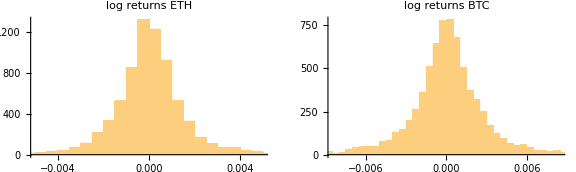

```mathematica
p1=Histogram[ethReturn,PlotLabel->"log returns ETH"];
p2=Histogram[btcReturn,PlotLabel->"log returns BTC"];
GraphicsRow[{p1,p2},ImageSize->Large]
```

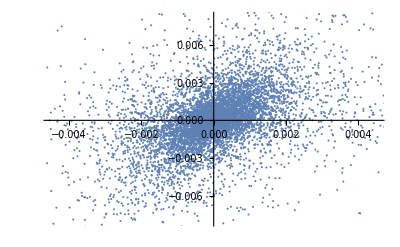

```mathematica
ListPlot[Transpose[{ethReturn,btcReturn}]]
```

```mathematica
paramsETH=FindDistributionParameters[
ethReturn,StudentTDistribution[μ1,σ1,ν1]];
paramsBTC=FindDistributionParameters[
btcReturn,StudentTDistribution[μ2,σ2,ν2]];
```

```mathematica
ℋ1=DistributionFitTest[
DeleteDuplicates@ethReturn,
StudentTDistribution[μ1,σ1,ν1],
"HypothesisTestData"]/.paramsETH;
ℋ2=DistributionFitTest[
DeleteDuplicates@btcReturn,
StudentTDistribution[μ2,σ2,ν2],
"HypothesisTestData"]/.paramsBTC;
```

```mathematica
Grid[{
{" ","Hypothesis Tests - "," "},
{" ","Student T Dist"," "},
{"ETH"," ","BTC"},
{ℋ1["TestDataTable",All],Spacer[100],ℋ2["TestDataTable",All]}},
Frame->True]
```

| Hypothesis Tests -  |  
  | Student T Dist |  
ETH |   | BTC
 | Statistic | P-Value
Anderson-Darling | 0.640432 | 0.610604
Cramér-von Mises | 0.0803075 | 0.690078
Kolmogorov-Smirnov | 0.0108149 | 0.36989
Kuiper | 0.0145532 | 0.464552
Pearson χ^2 | 73.9782 | 0.319019
Watson U^2 | 0.0611241 | 0.581955 |  |  | Statistic | P-Value
Anderson-Darling | 1.61585 | 0.151079
Cramér-von Mises | 0.254242 | 0.183023
Kolmogorov-Smirnov | 0.0137963 | 0.129239
Kuiper | 0.0246672 | 0.00463197
Pearson χ^2 | 99.7005 | 0.00918709
Watson U^2 | 0.253116 | 0.0135292

Copula Calibration

We next calibrate the parameters for the Gaussian copula by maximum likelihood, from which we derive the joint distribution for returns in the two indices via Sklar’s decomposition.

```mathematica
𝒟1=CopulaDistribution[{
"Multinormal",
{{1,ρ},{ρ,1}}},
{StudentTDistribution[μ1,σ1,ν1]/.paramsETH,
StudentTDistribution[μ2,σ2,ν2]/.paramsBTC}]
```

CopulaDistribution[{Multinormal,{{1,ρ},{ρ,1}}},{StudentTDistribution[4.98901×10^-7,0.000996648,2.53188],StudentTDistribution[0.0000614323,0.00176359,2.5074]}]

EstimatedDistribution does not like 7000 data pairs covering 25 days, unless it does. Ok.
There are three versions of 𝒟2 now. Raw time-step, medianBlocks and meanBlocks.

```mathematica
𝒟2=EstimatedDistribution[Transpose[{SP500returns,NASDAQreturns}],𝒟1,
ParameterEstimator->"MaximumLikelihood"]
```

CopulaDistribution[{Multinormal,{{1,0.701974},{0.701974,1}}},{StudentTDistribution[4.98901×10^-7,0.000996648,2.53188],StudentTDistribution[0.0000614323,0.00176359,2.5074]}]

It worked that time

𝒟2 = CopulaDistribution[{"Multinormal", {{1, 0.7014717756905754`}, {0.7014717756905754`, 1}}}, {StudentTDistribution[-7.918954615518965`*^-6, 0.0009013308668338338`, 2.1699438548707324`], StudentTDistribution[0.00005648792508095511`, 0.0016261826528475392`, 2.10071796720837`]}]

Changing the timescale of the samples (raw is 5 minute data)
MovingMap still results in about 7000 data points, the day average retains the five minute offset

```mathematica
Length@MovingMap[Median,ethReturn,Quantity[Round[24*12],"Events"]]
```

6908

Blocks of 12 are one hour step size

```mathematica
hb=1;
```

```mathematica
Length@Partition[ethReturn,hb*12,hb*12,{1},{}]
```

600

There are 600 one hour blocks in 25 days

medianBlocks = Transpose[{
    Median /@ Partition[ethReturn, hb*12, hb*12, {1}, {}],
    Median /@ Partition[btcReturn, hb*12, hb*12, {1}, {}]}];

meanBlocks = Transpose[{
    Mean /@ Partition[ethReturn, hb*12, hb*12, {1}, {}],
    Mean /@ Partition[btcReturn, hb*12, hb*12, {1}, {}]}];

𝒟2 = EstimatedDistribution[meanBlocks, 𝒟1,
  ParameterEstimator -> "MaximumLikelihood"]

CopulaDistribution[{Multinormal,{{1,0.827701},{0.827701,1}}},{StudentTDistribution[7.91895×10^-6,0.000901331,2.16994],StudentTDistribution[-0.0000564879,0.00162618,2.10072]}]

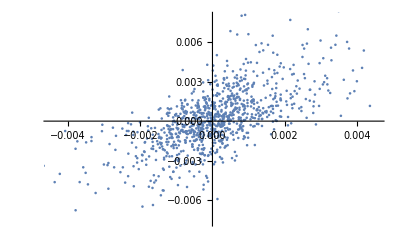

```mathematica
ListPlot[RandomVariate[𝒟2,10^3],PlotRange->Automatic]
```

Pairs Trading with the Copula Model

Once we have successfully fitted marginal distributions for the two series and a copula distribution to describe their relationship, we are able to derive the joint distribution. This means that we can directly calculate the joint probability of each pair of data observations. So, for instance, we find that the probability of a return in the ETH of 5% or more, together with a return in the BTC of 1% or higher, is approximately 0.2%:

```mathematica
Probability[eth>.05∧ btc>.01,{eth,btc}\[Distributed]𝒟2]
```

0.0000285726

```mathematica
Probability[eth>.001∧ btc>.005,{eth,btc}\[Distributed]𝒟2]
```

0.0337116

So the way we test our model is to calculate the daily returns for the two indices during the-out-of sample period from Jan 2016 to Feb 2017 and compute the probability of each pair of daily observations. On days where we see observation pairs with abnormally low estimated probabilities, we trade the pair accordingly over the following day.

In this analysis I pick a threshold probability level of 15% and assume we hold the trade for one day only, opening and closing the trade at the start and end of the day after we receive a signal.

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[5,"Days"]],
end=lastTick},
ethOutSamp=TimeSeriesWindow[ethTS,{start,end}]["Values"];
btcOutSamp=TimeSeriesWindow[btcTS,{start,end}]["Values"];
ethReturnOS=Log[Drop[ethOutSamp,1]]-Log[Drop[ethOutSamp,-1]];
btcReturnOS=Log[Drop[btcOutSamp,1]]-Log[Drop[btcOutSamp,-1]]
]
```

{0.00370038,0.00302732,0.00508098,-0.00338137,0.00210979,0.00481103,0.00458795,-0.0000267938,0.0111602,-0.00275216,0.00349742,-0.00145132,-0.00739397,0.00944219,-0.00281716,-0.000732503,-0.0011263,-0.00220045,0.00183241,-0.00168141,-0.00733437,0.00565493,0.000537595,-0.0010234,0.000285578,-0.00149831,0.00397487,0.00386881,-0.00291531,0.0022153,-0.0000812525,-0.00064628,0.00145533,-0.000701049,0.00540248,0.0036243,-0.00293613,0.000963749,-0.00231456,-0.000344563,0.000835756,-0.000115843,-0.00310097,-0.00352308,-0.00141659,0.00447978,0.000668262,0.000744026,-0.000771733,-0.00163218,0.000459602,-0.000651379,0.00191374,-0.000733731,-0.00159355,-0.00146347,-0.00147381,0.000929052,-0.00516968,0.00344536,-0.00202127,-0.00220378,0.000251175,0.00284389,0.000365101,0.000416336,0.00106793,0.00112145,-0.00192467,-0.00282487,0.00247682,-0.00185158,0.00120321,-0.00019149,0.00349899,-0.000263655,-0.000578548,0.00302376,0.000412565,-0.000467732,0.000537208,-0.000210438,-0.00183392,-0.00056225,0.000556865,0.000282899,-0.00069968,-0.000611205,0.000144139,0.000836135,0.00130789,-0.000700078,0.000298908,0.00162168,0.00129275,-0.00119535,-0.000798304,-0.000403323,-0.00193774,0.0002459,-0.00207841,0.000302073,0.000416312,0.000864389,-0.000454217,0.00119836,-0.00205348,-0.00118518,-0.000582171,0.00112357,0.000196322,-0.00121927,-0.000974447,0.000533245,-0.00416266,0.00177561,-0.000663783,0.00117548,-0.000555403,0.00141306,-0.00176899,-0.00218193,-0.000890587,0.00061119,-0.000401669,-0.000643002,0.0000651524,0.0016248,0.00284181,-0.00135761,0.000746714,-0.0013753,0.000629269,0.000633829,0.0023112,0.00158136,-0.0000815627,-0.000577753,0.00123616,-0.00100832,-0.000435557,-0.000200935,-0.00261664,-0.000274641,0.00104413,-0.000279007,0.00026187,0.00073719,0.00104256,0.00124079,-0.00115399,0.0000203036,-0.00194839,-0.00117437,0.000405082,-0.000499606,0.000381017,0.000443893,-0.000795022,0.00192736,-0.0000333478,-0.000515411,0.00399844,0.000903492,0.00117468,-0.000054169,0.00023813,-0.00146309,0.000274265,0.000850909,-0.000709061,-0.00140002,0.0000171033,-0.000483549,1.97026×10^-6,0.00043149,0.00114909,-0.000726289,0.00184866,0.000761297,0.000263514,-0.000263348,-0.000067408,0.000111658,0.00191762,-0.000740866,-0.00132467,0.00105492,0.000252539,-0.000160235,-0.0000791877,-0.0000383295,-0.00128676,0.000652408,0.000657164,-0.000667318,-0.00310107,0.000510809,-0.000163132,-0.000458117,0.00127713,-9.41154×10^-6,0.000263755,-0.00114528,0.000128327,0.000216551,-0.000165483,0.00076225,0.000294838,0.000247385,-0.000198821,0.000753184,0.0000243502,-0.000239107,0.0000775947,-0.000122819,0.000178951,0.000515741,-0.0000218635,0.00149435,0.00224158,-0.00162617,-0.000601492,-0.0013386,0.0046766,-0.000689499,0.00249552,0.00272907,0.00188026,0.00148983,0.00115892,-0.00247544,-0.000190333,7.7806×10^-6,0.000633538,-0.0000680401,-0.000312222,0.00273984,0.00156125,0.000108111,-0.00098128,-0.00061613,-0.00299333,0.00285948,-0.000432588,-0.00126967,0.0000351798,0.000652445,0.00152169,0.00236295,0.00332671,0.000737023,-0.00024623,0.00253512,-0.00261662,0.000355937,-0.000150969,0.00128803,0.00401461,-0.00158188,0.00179112,-0.00228449,-0.000567363,-0.00184077,-0.00129771,-0.000134856,0.000544924,-0.00306812,0.00111568,0.00140377,0.000889117,-0.000127099,-0.00143038,0.00124562,0.00191386,-0.000724746,0.00171547,-0.000233684,-0.00225153,0.00297258,-0.000769524,-0.000568085,0.0012371,-0.000975646,0.00118721,0.00163404,-0.000506308,-0.00130166,0.00128096,0.00114072,0.00100742,-0.00208659,0.00154682,0.000462387,0.000023598,-0.00178838,-0.00133657,0.000426682,-0.000412362,-0.00196608,-0.00109414,-0.000648325,-0.00386028,0.00282837,-0.000463457,0.00162217,-0.000304223,-0.00108821,-0.000397416,0.000219144,-0.000499811,0.00141308,0.00208795,-0.000527997,0.000262265,-7.49573×10^-6,-0.0001727,-0.000612554,-0.000319385,-0.00143041,0.000677374,-0.00238285,0.00124298,0.00152093,-0.000904526,-0.00212065,0.0018742,0.003354,-0.000700537,0.00188391,-0.000376318,0.000556098,-0.00073505,-0.000264944,-0.000790329,-0.000518748,-0.000358051,0.00079011,0.00102532,0.00053104,0.00141595,0.000532514,-0.0010328,0.00121511,0.00136356,-0.00017621,-0.000653478,0.000129933,-0.00128557,-0.0000716331,-0.0000244014,0.000811505,0.00268386,-0.00343648,0.0013833,0.0000673604,0.000183337,-0.000320051,0.00076137,0.00167054,-0.000229847,0.000725973,-0.000586346,0.00027156,0.000761904,-0.00334053,-0.0021073,0.000184574,0.000340525,-0.000265673,0.000605012,-0.00338882,0.00107657,0.00186001,-0.00159882,0.000892158,-0.000790684,-0.000147019,-0.0000120561,0.00135086,0.000221847,-0.000801026,0.000561043,0.000299454,-0.000177856,0.0000281348,0.000195016,0.000503087,0.000752664,0.000614362,0.000170567,-0.00318079,0.000748249,-0.00101716,-0.0000891561,-0.00355291,-0.00305595,0.000626989,0.00166971,-0.00355401,-0.00240387,-0.00302857,-0.00462602,0.000596682,0.000404818,-0.00345092,0.000872156,0.00443906,-0.00143632,-0.00409754,-0.00089576,-0.0327974,0.0133635,-0.00436907,0.00315322,-0.00498767,0.0146313,-0.00776735,0.00797626,-0.000689467,-0.00813303,0.00188705,0.00163647,-0.00238003,-0.00064151,-0.00559169,-0.000350032,-0.00230821,0.0106796,0.000197639,-0.000281957,0.00178158,0.00310779,-0.000820349,0.00147593,0.00738586,0.00254061,-0.00110887,0.00110297,0.00643186,-0.00279476,0.00416526,0.00200243,-0.000632415,-0.00158593,-0.00232092,0.000936143,-0.00163887,-0.000506056,0.000569359,-0.00154965,-0.00170436,0.00285463,0.00253126,0.00192836,-0.00211696,-0.00161715,0.000682292,0.00207786,0.00165316,0.000390821,0.00287314,-0.000574745,-0.000485352,0.00244684,0.00080043,0.00428086,-0.00205318,0.00012013,-0.0000766619,0.000134507,0.00166458,0.00225557,-0.000788878,-0.00150806,-0.00151086,0.000900135,-0.00165261,-0.00159288,0.00286925,-0.00121069,-0.00205633,0.000157877,0.000993044,-0.00057264,0.00027494,0.00277592,0.00199288,-0.00132475,0.00016523,-0.0023711,0.00172757,0.00100375,-0.00104685,-0.000619506,0.000126124,-0.000117062,-0.00173559,0.000248316,0.000379732,-0.000228173,0.0000621689,0.000293562,-0.000861842,0.000425458,0.000339669,0.00146287,0.000303235,0.00272343,-0.000999988,-0.000150032,-0.0018779,0.00233448,0.00075269,0.00135536,0.0000476687,0.00234943,-0.000734319,0.0000870716,-0.000075713,0.000310323,-0.00147198,-0.000186492,-0.00290255,0.000324478,0.00107557,0.0000647839,0.000544222,-0.000271792,0.000748933,0.00132591,-0.0000238329,-0.00080922,-0.00163329,0.000109572,-0.0000582764,0.00147491,0.000426471,-0.000063558,0.000076662,-0.000143996,0.00156395,-0.000642049,0.0000505144,0.00267937,0.00853645,-0.00295445,0.00413356,-0.00215922,-0.000628022,0.000838565,0.00058439,0.000329177,0.00403008,-0.00165845,-0.000267911,0.00013685,-0.00164153,0.00102167,0.0000114995,-0.0015611,0.00053301,-0.0010439,0.000574088,0.000192916,-0.000778444,0.00162178,-0.00052417,-0.000977828,-0.00782391,-0.000508026,0.00201586,0.00203724,0.00065412,-0.00129116,0.00076454,0.00096179,-0.0015731,0.000833935,-0.000462727,0.00202395,0.00101793,-0.00069766,-0.00320497,0.00127186,0.000799201,0.000295333,-0.00179919,-0.000306661,-0.00103913,0.000563073,0.000510324,-0.00012586,-0.00254671,-0.00334761,0.00162693,0.000984469,0.000992218,-0.00142184,-0.000553615,0.000133484,-0.000693514,-0.00273335,-0.000321035,-0.00200698,-0.00630959,-0.00589107,0.000750924,0.00770452,-0.00297586,0.000915069,0.000673088,-0.00390719,-0.00103714,-0.00198605,0.00365744,0.00189766,0.00197652,-0.00106934,0.00118282,0.00518788,0.000787237,0.000830986,-0.000982922,-0.000378182,-0.001465,-0.00605755,0.0011135,0.000590839,-0.000330723,0.00058276,-0.00291697,-0.00486009,0.00238329,0.000836548,0.0000484662,-0.00615396,-0.0000341877,-0.00436578,0.00372355,-0.00256993,-0.00142154,-0.00347855,-0.0051738,0.0102241,0.000847963,-0.00100657,0.00493691,0.00174131,0.00152369,-0.00102366,-0.00317187,-0.000917204,-0.00456757,0.00577883,0.00242703,-0.00300177,0.00318474,0.000266986,0.000841933,0.0045481,0.00183541,-0.00226808,-0.00324968,0.000771949,0.00120879,-0.000602443,-0.00141487,-0.0009882,-0.00536569,0.000215171,0.00262557,0.000300652,0.000938106,-0.000585996,0.00273086,0.00145504,-0.000783647,0.00080824,0.00249156,-0.000398191,0.000982937,-0.000994048,-0.000411057,-0.00516343,0.00120977,0.00317677,-0.0000231208,-0.000695664,-0.000329483,0.00290761,0.00130772,-0.00116812,-0.00161501,0.000538779,-0.000303439,-0.00201331,0.00142651,0.000300157,0.000408526,0.00179012,0.0000352448,-0.00175792,0.000107816,0.00229446,-0.00214347,-0.00119843,-0.00151806,-0.000132611,0.000326481,-0.004415,0.00354509,0.000162278,0.000914481,-0.000491338,0.00366205,0.000691304,-0.002896,-0.000444075,0.000785057,-0.000601321,-0.00150949,0.000903745,-0.000459951,0.000126713,-0.000362835,0.000128763,0.000245406,-0.001442,-0.000429418,0.000758779,0.00154451,0.000176076,0.00129833,0.00118534,-0.000360681,-0.000564789,0.00209004,-0.000597808,-0.000263819,0.00437962,0.00145193,-0.000109033,0.000196999,-0.000629366,0.00116381,-0.0000494657,-0.000391887,-0.00218663,0.000149588,0.00403863,0.000218797,0.000731096,0.00176993,0.0021969,0.000167227,0.0011239,-0.00165152,-0.0003534,0.000759883,-0.000558025,-0.00078531,0.000139952,0.00097813,0.00122752,0.00087225,-0.00114176,-0.0011873,-0.000318403,-0.00022492,0.000423104,-0.000893601,-0.000255602,-0.00226824,0.000644012,0.00118618,-0.000633258,0.000230408,0.00149925,0.00124372,-0.000940613,0.00125073,-0.000244021,0.00234009,-0.000306802,0.0010846,-0.000467348,-0.000698325,-0.000962036,-0.00109385,0.00190096,0.000159471,-0.000093811,-0.0000584255,-0.000106791,-0.000513057,0.000731152,-0.00209612,-0.00173888,0.000860051,-0.00211076,0.000349495,-0.0000128678,-0.000261033,0.00180491,-0.000825429,0.00101946,-0.000515193,-0.000132205,-0.0000615972,-0.000116999,-0.00150383,-0.00326448,0.000677928,-0.000669088,0.00190361,0.000121243,-0.00128669,0.0000653538,-0.00331529,-0.000406459,-0.00233423,0.000701345,0.00125548,-0.000454811,-0.00177314,-0.00516302,0.00169552,0.000891739,0.00361399,-0.000211706,-0.000632331,0.0034034,-0.00144732,0.00205946,0.00169426,-0.00157617,-0.00157168,-0.000613292,0.00113137,0.00164241,0.000494873,0.00352072,-0.00104681,-0.000439622,-0.000177576,0.000183502,-0.00181567,0.00152784,-0.00131771,-0.00425073,0.00213863,-0.00341988,0.000542334,7.51208×10^-6,0.00128299,-0.000258568,-0.00119017,0.00043929,0.00163257,0.00160809,0.000635904,-0.000692074,-0.00129195,-0.0023141,-0.00323637,0.0013312,-0.00308521,0.00268122,-0.00113697,-0.000719052,0.000132688,-0.00233295,-0.00292131,0.00137833,-0.00063825,0.00107059,-0.000708337,0.00217736,-0.00212718,0.00100974,-0.000249545,0.00196452,0.00137346,0.000850891,-0.00152488,-0.000237556,0.000880677,0.000716827,0.00222146,-0.00036204,0.00152389,-0.000458737,-0.00162464,0.00119305,0.000650677,-0.000818794,0.000515537,-0.000551031,-0.00125853,0.000552405,0.00100721,0.000549054,0.00251818,-0.000718678,-0.00107779,0.000228888,0.000344082,0.000295581,0.000818437,-0.00249785,-0.0000321004,-0.000144587,0.000947387,-0.000274705,0.00015301,0.00012971,-0.000187357,-0.000538753,0.0012935,0.0029048,0.00224451,0.000589775,0.000354829,-0.00111606,0.000919529,-0.000411202,-0.000449424,0.000135256,-0.0000422487,0.00327159,-0.000177129,-0.00019462,0.00128406,0.000425828,-0.00233186,-0.00204003,0.00124144,0.000122615,-0.00141922,-0.00118412,0.000804995,-0.0000853776,-0.000318086,0.000249361,0.00140926,-0.000310244,0.00232843,0.0011386,0.0000569683,-0.0000967123,-0.000272719,-0.00337495,0.00162737,0.000200706,-0.00373341,0.00163527,0.000167172,-0.00172134,0.00127188,0.000152889,-0.00190871,-0.000553862,-0.000587518,-0.000443773,-0.00129643,-0.000119643,-0.000400047,0.000429614,0.00173615,0.000613133,0.000914722,-0.000529839,-0.000128198,0.000502857,0.00206461,-0.000401113,0.000461476,-0.000468322,-0.000681135,-0.00197473,0.000918195,-0.00403998,-0.000445809,-0.000106392,0.00139959,-0.000794271,0.0011768,-0.000285466,0.0000509176,-0.000189618,0.000802663,-0.0000848618,-0.000700275,-0.000444212,0.0000193181,-0.000929683,0.00121,0.0000350302,0.000757921,-0.00027964,-0.000114684,0.000218013,0.00123659,0.000630698,0.00234843,0.00173489,-0.00149983,0.000741187,0.00216792,-0.000595502,-0.00102142,-0.00111815,-0.000512111,0.000705642,-0.00042273,0.000134086,-0.00069808,0.00269698,0.000694151,0.000561723,-0.000885766,0.000351128,-0.00169015,-0.000290395,-0.000559502,0.00109469,0.000816823,0.000135116,-0.000339967,0.0000429126,-0.000337128,-0.00196342,-0.00227414,-0.00147444,0.00249048,0.00015396,-0.00725287,-0.00171668,-0.000187249,-0.00253821,0.000238701,-0.00224988,0.00232638,0.00191543,0.000150082,0.00107852,0.00208979,0.00074128,0.00232345,-0.000233343,-0.00135178,0.000633798,-0.0000865295,-0.000573214,-0.000112145,-0.00247645,-0.000253072,-0.000285993,0.000452062,0.00102573,0.000774098,0.0000565236,-0.000312434,-0.000416806,0.000866007,0.00132638,-0.000751268,-0.00252635,-0.000382371,-0.000412324,-0.00326476,-0.000805544,-0.000779591,-0.00127767,0.00101363,0.00325526,0.00130556,-0.000958784,-0.00236791,0.00109279,0.00124342,0.000262233,-0.000567184,0.00148463,0.000567854,0.00126287,-0.00106394,0.000567193,0.00210632,-0.00376105,-0.000058073,0.000709923,0.000426981,0.000946802,0.000123475,0.000428408,0.00164243,-0.000798425,0.0000283518,-0.0000374668,0.000235924,0.0033402,-0.0000331477,0.000208324,0.00209513,-0.000468038,-0.00258349,0.00117772,-0.000535521,0.000220942,-0.0000285504,-0.00143447,0.000627382,0.000240566,-0.0015839,-0.00018363,0.000257518,0.0015939,0.000627631,-0.00289263,-0.000494609,0.0015051,-0.000431564,-0.00172429,0.000773975,0.000757476,-0.0010167,0.000293953,0.000601653,-0.000646415,0.000933036,0.00170826,-0.000576346,-0.00288718,0.000525726,-0.00160891,0.000293296,0.000485116,-0.000143551,-0.000544787,0.00134195,0.0000193578,0.00111008,-0.000665454,-0.000596927,0.0000147293,-0.000676179,0.000386093,-0.00111424,0.000241289,-0.000860227,-0.00123002,0.000733715,-0.00122639,0.000708297,-0.000458825,-0.00136049,0.00196458,0.00219963,-0.00146205,-0.000916195,0.000664388,0.000350508,2.28189×10^-6,-0.000575677,-0.000182848,-0.000221317,-0.00135951,0.000063858,0.00161,-0.00107607,0.000535787,0.000382882,0.000313177,0.00142264,0.000545333,-0.00148603,0.000251962,-0.000919342,0.000279704,0.000297204,-0.000833795,0.000606193,-0.000775967,-0.0000700405,0.000285995,0.000157077,0.000486941,0.0020097,-0.0004029,0.0018522,-0.000915833,0.000746947,-0.00011482,0.000480061,-0.00090633,-0.000966968,0.000293013,0.000111805,-0.000154446,0.0000167033,-0.000111268,0.000880478,-0.000231927,-0.000832034,-0.000489814,0.00057138,0.000815917,-0.000496679,0.000370301,0.000271157,-0.00151472,0.0000589863,-0.000360148,-0.000271584,-0.00192199,-0.000686739,0.000221246,-0.0011684,0.000333303,-0.00429517,0.000487058,-0.00318492,0.003069,0.000445614,-0.0023261,0.00079565,-0.00215908,-0.00277495,-0.00070037,-0.00136807,0.00104714,-0.000531355,0.00243534,0.00216529,-0.000276943,-0.000254021,-0.00330949,0.000251748,-0.00218195,-0.000230351,-0.00172597,-0.000893541,-0.00323275,-0.0016162,0.00241844,0.00180757,-0.00462259,-0.00255124,-0.00017029,-0.000766284,-0.0023049,-0.00471226,0.0081013,-0.00087129,0.00397253,0.00327369,0.00078122,-0.00156643,0.000456425,0.00279577,0.00126164,-0.00127582,-0.000535014,-0.000116908,0.00372825,0.000983994,0.000301277,0.00301973,0.000292758,0.000468854,0.000749271,-0.00168481,0.0000135984,-0.00368255,-0.000486514,0.000995537,0.00104389,0.00078896,-0.00302526,-0.001884,0.0000870614,-0.00230526,0.00159954,-3.43969×10^-6,0.00273063,0.00035255,0.00137974,-0.00151921,0.00138017,0.000644679,-0.000994431,-0.00101391,0.000720151,0.000151759,0.00110691,0.0000742477,0.00100379,0.000945167,0.000191128,0.00119127,-0.000709452,0.000965414,0.0000760495,0.00137586,0.00248255,-0.00137444,-0.0014787,0.0019009,-0.000944693,0.00227621,0.000322326,0.00126096,0.00344452,0.000698886,0.000032195,-0.0019966,0.00074082,-0.000519344,-0.00105216,0.00222693,0.000669171,-0.000205041,0.000776418,0.00626166,-0.000783578,0.00287949,0.0023041,0.00450669,0.00436935,-0.00424446,-0.00337127,0.00420613,-0.000246958,-0.00210689,-0.000708741,-0.00360222,-0.00106367,0.000137901,-0.00136332,-0.00454859,-0.00154838,-0.000456263,-0.00561057,0.00200707,0.0043475,-0.00145485,0.00135976,-0.00077844,0.000062086,0.00438133,-0.00022942,-0.0024008,-0.000614866,-0.00171053,0.00157059,0.00105808,0.000605057,0.00122189,0.000423437,-0.0010316,0.000169552,-0.00164259,0.000140416,0.00128899,0.00223453,0.000955019,0.00352029,-0.00160061,-0.000310631,0.00170204,0.00144363,-0.000922082,0.00100652,-0.00123683,-0.00271765,0.0000720935,-0.000893894,0.000889071,0.000514337,0.00126495,-0.00223172,-0.00191455,0.000122369,-0.00127806,-0.00163685,-0.00134514,-0.000174943,0.0010209,-0.00069386,-0.000292516,0.00128871,-0.000159111,-0.000135695,0.0000505966,0.0008365,0.000344803,-0.000474668,0.000706311,0.00164427,-0.000592336,-0.000259278,-0.0013676,-0.000856293,-0.00111546,-0.00191435,0.000415904,0.000356535,0.00122411,-0.000767346,0.000590252,0.000324758,-0.000385849,0.00231978,0.000448342,0.000319302,-0.0000604387,-0.00186131,-0.000241026,-0.00130336,0.00050077,-0.000484645,0.00107425,-0.000640376,-0.000801712,-0.000450166,-0.000284847,-0.000340856,-0.00102563,0.000314005,0.00257202,-0.000111164,0.000600726,-0.000471766,0.000606916,0.000243611,-0.000675456,-0.000612802}

```mathematica
Length/@{ethOutSamp,btcOutSamp}
```

{1440,1440}

Next, we use the estimated joint distribution to compute the probability of each daily observation of index returns. We gather the daily returns series and associated probability series into a single temporal variable:

```mathematica
Probability[x>ethReturnOS[[1]]∧ y>btcReturnOS[[1]],{x,y}\[Distributed]𝒟2]
```

0.0713361

```mathematica
Probability[x>ethReturnOS[[2]]∧ y>btcReturnOS[[2]],{x,y}\[Distributed]𝒟2]
```

0.104387

```mathematica
probs=Table[
{
ethReturnOS[[i]],
btcReturnOS[[i]],
Probability[x>ethReturnOS[[i]]∧ y>btcReturnOS[[i]],{x,y}\[Distributed]𝒟2]
},
{i,1,Length[ethReturnOS]}];
```

These are five minute ticks, going back five “Days” makes them look like Days instead. Fixed.

```mathematica
Length@DateRange[DatePlus[lastTick,-Quantity[5,"Days"]],lastTick,Quantity[5,"Minutes"]]
```

1441

```mathematica
tdProbs=TemporalData[Transpose[probs],
{DatePlus[lastTick,-Quantity[5,"Days"]],Automatic,Quantity[5,"Minutes"]}]
```

TemporalData[…]

We plot the time series of index returns and associated probabilities as follows:

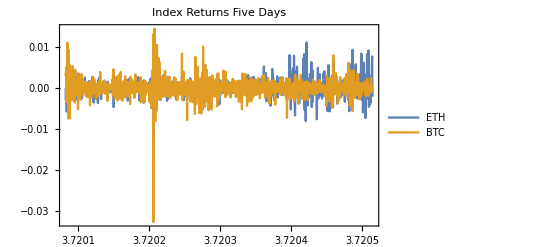

```mathematica
DateListPlot[tdProbs["Paths"][[{1,2}]],
PlotLegends->{"ETH","BTC"},
PlotLabel->"Index Returns Five Days",
PlotRange->All]
```

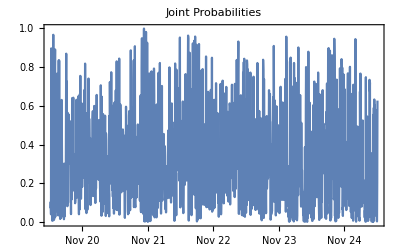

```mathematica
DateListPlot[tdProbs["Paths"][[3]],
PlotLabel->"Joint Probabilities"]
```

Trade Signal Generation

The table below lists the index returns and joint probabilities over the first several days of the series. The sequence of trade signals is as follows:

After a very low probability reading for 2016/1/4, we take equally weighted positions short the S&P500 Index and long the Nasdaq index on 2016/1/5.  We close the position at the end of the day, producing a total return of 0.44%. 

Similar signals are generated on 2016/1/6, 2016/1/7, 2016/1/8, 2016/1/13 , 2016/1/15 and 2016/1/20 (assuming a 15% probability threshold). We take the reverse trade (Buy the S&P500, Sell the Nasdaq) on only one occasion in the initial part of the sample, on 2016/1/14.

```mathematica
sampleDates=Take[Flatten@tdProbs["DateList"],12]
```

{Sun 19 Nov 2017 12:19:11GMT-6.,Sun 19 Nov 2017 12:24:11GMT-6.,Sun 19 Nov 2017 12:29:11GMT-6.,Sun 19 Nov 2017 12:34:11GMT-6.,Sun 19 Nov 2017 12:39:11GMT-6.,Sun 19 Nov 2017 12:44:11GMT-6.,Sun 19 Nov 2017 12:49:11GMT-6.,Sun 19 Nov 2017 12:54:11GMT-6.,Sun 19 Nov 2017 12:59:11GMT-6.,Sun 19 Nov 2017 13:04:11GMT-6.,Sun 19 Nov 2017 13:09:11GMT-6.,Sun 19 Nov 2017 13:14:11GMT-6.}

```mathematica
sampleProbs=Take[Transpose[tdProbs["ValueList"]],12]
```

{{0.0000166656,0.00370038,0.0713361},{-0.00278423,0.00302732,0.104387},{-0.00101995,0.00508098,0.0402578},{-0.00261314,-0.00338137,0.89627},{-0.00081661,0.00210979,0.170103},{-0.00574909,0.00481103,0.0450389},{-0.000754405,0.00458795,0.0494168},{-0.00520624,-0.0000267938,0.518025},{-0.000291605,0.0111602,0.00675775},{-0.00303718,-0.00275216,0.875605},{-0.00158037,0.00349742,0.0821194},{0.00105764,-0.00145132,0.18749}}

```mathematica
PaddedForm[TableForm[Chop[sampleProbs,10^-5],
TableAlignments->Right,
TableHeadings->{
Table[DateString[sampleDates[[i]],"ISODate"],{i,1,12}],
{"ETH","BTC","prop"}}],{3,4}]
```

| ETH | BTC | prop
2017-11-19 |  0.0000 |  0.0037 |  0.0713
2017-11-19 | -0.0028 |  0.0030 |  0.1040
2017-11-19 | -0.0010 |  0.0051 |  0.0403
2017-11-19 | -0.0026 | -0.0034 |  0.8960
2017-11-19 | -0.0008 |  0.0021 |  0.1700
2017-11-19 | -0.0057 |  0.0048 |  0.0450
2017-11-19 | -0.0008 |  0.0046 |  0.0494
2017-11-19 | -0.0052 | -0.0000 |  0.5180
2017-11-19 | -0.0003 |  0.0112 |  0.0068
2017-11-19 | -0.0030 | -0.0028 |  0.8760
2017-11-19 | -0.0016 |  0.0035 |  0.0821
2017-11-19 |  0.0011 | -0.0015 |  0.1870

Pairs Trading Strategy Results

We are now ready to apply the trading algorithm to the entire sample and chart the resulting P&L.

```mathematica
α=0.15;
signals=HeavisideTheta[#-(1-α)]-HeavisideTheta[α-#]&/@tdProbs["ValueList"][[3]]
```

{-1,-1,-1,1,0,-1,-1,0,-1,1,-1,0,1,-1,0,-1,-1,0,0,0,1,-1,0,0,0,0,-1,-1,0,0,0,0,0,0,-1,-1,0,0,0,0,-1,0,-1,-1,-1,-1,0,0,0,0,0,0,0,0,-1,0,0,-1,0,-1,0,-1,0,-1,0,0,0,0,0,1,-1,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,-1,0,0,0,-1,0,0,0,-1,-1,-1,0,-1,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,-1,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,-1,0,-1,-1,-1,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,-1,-1,0,0,-1,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,0,-1,0,0,-1,0,0,0,0,0,0,-1,-1,0,0,0,-1,-1,0,-1,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,-1,-1,0,0,0,0,0,0,-1,0,-1,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,1,-1,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,-1,0,-1,0,1,0,0,1,0,-1,0,1,0,1,-1,1,-1,-1,-1,0,-1,0,1,0,0,-1,0,1,0,0,-1,0,0,-1,-1,0,-1,-1,-1,0,0,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,-1,-1,-1,0,-1,0,0,-1,-1,-1,0,-1,0,0,-1,-1,0,0,0,0,0,0,-1,0,0,0,0,0,-1,-1,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,-1,-1,0,-1,0,0,0,0,0,-1,0,0,0,0,-1,0,0,-1,-1,0,-1,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,0,0,0,-1,0,0,0,0,0,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,-1,0,-1,0,1,0,0,-1,-1,-1,0,-1,-1,-1,-1,0,0,0,1,0,0,0,0,1,1,-1,0,0,1,0,0,-1,0,0,1,0,-1,0,-1,-1,0,-1,0,1,0,1,-1,-1,0,-1,0,-1,-1,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,-1,0,0,0,0,1,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,-1,0,-1,0,0,0,-1,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,-1,-1,0,0,-1,-1,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,0,0,-1,-1,0,-1,0,0,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,-1,0,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,-1,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,-1,0,-1,0,-1,-1,-1,0,0,0,-1,0,-1,-1,-1,-1,0,-1,-1,-1,0,0,0,-1,0,0,0,-1,-1,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,-1,0,0,0,0,0,0,-1,1,0,-1,0,0,0,0,0,0,-1,0,-1,0,0,-1,0,0,-1,0,0,-1,-1,0,-1,-1,-1,0,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,-1,-1,0,0,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,-1,-1,-1,-1,0,-1,-1,-1,-1,0,0,-1,0,0,-1,0,0,-1,-1,-1,0,0,0,0,0,-1,-1,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,-1,0,0,0,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,0,0,0,0,0,-1,-1,0,-1,0,0,1,0,0,0,0,0,0,-1,0,0,0,0,-1,-1,-1,0,-1,-1,-1,0,-1,0,0,-1,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,-1,-1,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,0,0,0,0,-1,-1,0,0,1,0,1,-1,0,1,0,0,1,0,-1,0,-1,-1,-1,0,0,1,0,0,0,0,0,0,0,-1,-1,1,1,0,-1,0,-1,-1,0,-1,-1,0,0,-1,-1,0,0,-1,-1,-1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,-1,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,-1,0,0,-1,-1,0,-1,0,-1,-1,-1,0,-1,0,0,0,0,0,0,0,1,0,-1,-1,-1,-1,0,-1,0,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,-1,-1,-1,0,0,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,0,0,0,0,0,0,0,-1,-1,-1,-1,0,0,-1,-1,0,-1,-1,-1,-1,0,-1,0,0,0,0,0,0,-1,0,0,-1,-1,0,0,-1,-1,-1,0,0}

```mathematica
Tally@signals
```

{{-1,408},{1,39},{0,992}}

A negative signal is when prob is below 0.15, then the next day is a trade

```mathematica
HeavisideTheta[0.0211-(1-α)]-HeavisideTheta[α-0.0211]
```

-1

A positive signal prob above (1 - ρ) or 0.85, that comes from a high joint probability

```mathematica
HeavisideTheta[0.8930-(1-α)]-HeavisideTheta[α-0.8930]
```

1

```mathematica
Part[Transpose@{signals,-signals},1]
Part[Transpose@tdProbs["ValueList"][[1;;2]],2]
%%*%
Total[%]
```

{-1,1}

{-0.00278423,0.00302732}

{0.00278423,0.00302732}

0.00581155

```mathematica
ptReturns=Total@Transpose@(Most@Transpose@{signals,-signals}*Rest@Transpose@tdProbs["ValueList"][[1;;2]])
```

{0.00581155,0.00610093,-0.000768231,-0.00292639,0.,0.00534235,0.00517945,0.,0.000285018,-0.00507778,-0.00250896,0.,-0.00933952,-0.00188132,0.,-0.00556627,-0.00188032,0.,0.,0.,-0.00482939,0.000580278,0.,0.,0.,0.,0.00314558,-0.00192145,0.,0.,0.,0.,0.,0.,0.00446033,-0.00136525,0.,0.,0.,0.,-0.000115843,0.,-0.00573358,-0.00545983,0.00304781,0.00359961,0.,0.,0.,0.,0.,0.,0.,0.,-0.00245954,0.,0.,-0.00583029,0.,-0.00259754,0.,-0.0000848733,0.,-0.000655477,0.,0.,0.,0.,0.,-0.00305365,-0.000820297,0.,0.,0.,0.00233072,0.,0.,0.000195264,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000911668,0.,0.,0.00161691,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00019495,-0.0000358487,0.,0.,0.,0.,0.,-0.000825616,0.,0.,0.,-0.00184143,0.,0.,0.,-0.00191403,-0.00344443,-0.000875233,0.,0.00153554,-0.000527557,0.,0.,0.,0.,0.,0.00229885,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000346413,0.,0.,-0.00341286,0.00104973,-0.00066936,0.,0.,0.000559153,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00076275,0.,0.,-0.0000923963,0.,0.,0.,0.,0.,0.,0.,-0.000498498,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000381137,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00151946,0.,-0.000625076,0.,0.,0.,0.00392596,0.,0.00272627,0.000445998,-0.000730331,0.00134049,0.,0.,0.,0.,0.,0.,0.,0.00250054,0.,0.,0.,0.,0.,-0.000256904,0.,0.,0.,0.,0.,0.00171199,0.00102587,0.,0.,-0.00346834,0.,0.,0.000395159,0.00199407,-0.00134195,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00130388,0.,-0.00184523,-0.0018915,0.,-0.000582942,0.,0.,-0.00111022,0.,0.,0.,0.,0.,0.,-0.000120121,0.00094776,0.,0.,0.,-0.00405644,0.000719843,0.,-0.000612598,0.,0.,0.,0.,0.,0.000325776,0.,-0.00120184,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000920668,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00221384,-0.00322716,-0.00125688,0.000941404,0.,0.,0.,0.,0.,0.,0.00152117,0.,-0.00123043,-0.00122152,0.,0.,0.,0.,0.,0.,0.000333695,0.,0.,0.,0.,0.,0.,0.000215343,0.,0.,0.,0.000439504,0.000302699,-0.0020476,0.,0.,0.,0.,0.,0.0000156524,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000592308,0.,0.,0.,-0.000518621,-0.0037855,0.,-0.00184657,0.,-0.00462921,0.,0.,0.0000220647,0.,-0.000168281,0.,-0.00652055,0.,-0.0144407,0.00389833,-0.00503776,-0.0108078,0.0159227,-0.00751113,0.,-0.00037791,0.,-0.00372976,0.,0.,0.000317644,0.,-0.00348484,0.,0.,-0.000775785,0.,0.,-0.00104308,0.000194656,0.,0.00339206,0.000908584,0.000573325,0.,0.,-0.00175095,0.,-0.000148487,0.00223188,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000383921,0.00169976,0.,0.,0.,-0.00114127,-0.000241169,0.000446322,0.,-0.00136647,0.,0.,-0.000930804,0.0020295,-0.00166224,0.,0.0010898,0.,0.,0.000811343,-0.000876672,0.,0.,0.,0.,0.,0.,-0.000741308,0.,0.,0.,0.,0.,0.000781884,0.000820958,-0.00122553,0.,0.,0.,-0.000358874,-0.00219333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000447498,-0.00017447,0.,-0.00182507,0.,0.,0.,0.000287992,0.,0.,0.,-0.00070718,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00077763,-0.00172789,0.000574887,0.,0.000581898,0.,0.,0.,0.,0.,0.000228153,0.,0.,0.,0.,-0.00149032,0.,0.,0.00564636,-0.00289229,0.,-0.00010813,0.,0.,0.,-0.000188933,0.,0.00122484,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00107443,0.,0.00162762,-0.000249182,0.,0.,0.,-0.0014234,0.,0.,0.,0.,0.,0.,-0.00116883,-0.000303808,0.00201135,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00285262,-0.00140969,0.,-0.00344941,0.,0.00140847,0.,0.000626119,0.,0.,0.0012236,0.001073,-0.000699816,0.,0.00471771,-0.00175662,-0.000315999,-0.000304698,0.,0.,0.,-0.00124749,0.,0.,0.,0.,0.00192084,-0.00259769,0.00132599,0.,0.,-0.0029221,0.,0.,-0.00182983,0.,0.,0.00456893,0.,0.000784071,0.,0.00151216,0.0013351,0.,0.000320585,0.,-0.000141182,0.,-0.0042627,0.00267401,-0.00254373,0.,-0.000600922,0.,0.00200038,-0.000168915,-0.00119061,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000302891,0.,0.,0.,0.00100143,0.,0.,0.,-0.000378849,0.,0.,0.,0.,-0.00130935,0.,0.000126174,0.,0.,0.,0.000523441,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.24672×10^-6,0.,0.,0.,-0.00145908,0.,0.,0.,0.,-0.00301688,0.,-0.000813813,0.,0.,0.,0.0000493019,0.,0.,0.,0.0033444,0.,0.000854395,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00159721,0.,0.,0.000728326,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00137349,0.000573366,0.,0.,-0.00103509,0.000227178,0.,0.,0.,0.,0.,0.,0.00106512,0.,0.,-0.000114767,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00100103,0.,0.,0.,0.,0.000749417,0.,0.,0.,0.,0.,0.,0.000467021,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000337961,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00153511,0.,0.00202369,-0.000682524,0.,0.,-0.00292865,0.0023039,0.,-0.0015844,0.,0.,0.,0.,0.,0.,-0.00241753,-0.000283767,0.,0.,0.,0.,-0.000467698,0.,0.,-0.0019195,0.,0.,0.,-0.000302315,0.,0.,0.,0.,-0.0000134432,0.,0.,-0.000102835,0.,0.,0.,0.,-0.00151216,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000841819,0.,-0.000748808,0.,0.00113931,0.,-0.00122869,0.,0.,0.,0.,0.00121587,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000852673,0.,0.,-0.00055639,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.000942799,0.,0.00109341,0.,0.000361621,0.,0.00253632,0.000516875,0.00072938,0.,0.,0.,-0.00155469,0.,-0.00412148,-0.00541316,0.00397246,0.000124531,0.,-0.00156366,-0.00330871,-0.0000260265,0.,0.,0.,0.000304778,0.,0.,0.,-0.00238346,-0.00050015,0.,-0.00210685,0.00335841,0.,-0.000370819,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00176941,0.00215967,0.,-0.00136712,0.,0.,0.0025816,0.,0.,0.,0.,0.,0.,-0.00161596,-0.00113825,0.,0.00231537,0.,0.,0.,0.,0.,0.,0.00146433,0.,0.00180425,0.,0.,0.00102792,0.,0.,-0.000963874,0.,0.,0.0000946941,0.000234622,0.,0.00092305,-0.00412984,0.00125567,0.,-0.000538114,0.,0.,0.,0.,0.,0.,0.,0.,0.000620972,0.,0.,0.,0.,0.,0.,0.,0.000427039,0.,0.,0.,0.,0.,0.,0.,0.,0.000049405,0.,-0.000117662,0.,0.,0.,0.,0.,0.000524093,-0.000254594,0.,0.,-0.00130303,-0.00578115,-0.00198037,-0.00931055,-0.00346505,-0.00427805,0.000597826,0.,0.,0.,0.,0.,-0.00144279,-0.000663277,-0.00305623,0.00138539,0.,-0.00403836,-0.00300317,-0.00477902,-0.00181439,0.,0.,-0.00193816,0.,0.,0.00467238,0.,0.,-0.00293381,-0.00320444,-0.00154141,0.,0.,0.,0.,0.,-0.00241569,0.00234222,0.,0.,0.,-0.00138457,0.00102491,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0030185,0.00158654,0.,0.,-0.00109127,0.,0.,0.,-0.000916661,0.,-0.00328769,-0.0029163,-0.00712456,-0.0049606,-0.00457139,-0.00299249,-0.00677488,0.00586703,0.,-0.00835766,-0.000697775,0.0023978,0.,0.,0.,0.,0.,-0.0106244,0.00270094,0.,0.00523821,0.,0.,-0.00467683,0.,0.,0.,0.,0.,0.,0.000131333,0.,0.,0.,0.,-0.00423034,-0.0019281,-0.00191258,0.,-0.00729535,-0.00760741,0.00533618,0.,0.00209221,0.,0.,0.000411267,0.00314318,0.,0.,0.,-0.00109927,0.000167999,0.,0.,0.,0.,0.,0.,0.,0.,0.00117507,0.,0.,0.,0.,0.,0.,0.,-0.0022772,-0.00584609,0.0000465867,0.,0.,0.,0.,0.,0.,0.,-0.00162338,-0.00151771,0.,-0.000209801,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00279701,-0.00348723,-0.00287615,-0.00155463,-0.00571106,0.00203015,0.,0.,0.,0.,-0.00241074,-0.000679247,0.,0.,-0.00228378,0.,-0.00528564,0.00356768,0.,-0.00637799,0.,0.,-0.00242032,0.,0.0027334,0.,-0.000959821,0.000274419,0.00248097,0.,0.,-0.00231812,0.,0.,0.,0.,0.,0.,0.,0.000955316,-0.000386176,0.000110309,-0.00155135,0.,-0.00268846,0.,0.00488246,0.00027238,0.,0.00319333,0.00204347,0.,0.,0.00145557,0.00166107,0.,0.,-0.00183349,0.000969908,0.000216312,0.,0.0012738,-0.000399455,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00203851,0.000185325,-0.000692355,0.,0.,0.,0.000363423,0.,0.,0.,0.,0.,0.,0.,-0.0000528007,0.,0.,-0.00173263,0.,0.,0.,0.,-0.000558461,0.,0.,0.,0.,0.,0.,0.,-0.000806745,-0.000708842,0.,0.,0.,0.,0.,0.000234247,0.,0.,0.00512273,0.00202491,0.,0.00623848,0.,0.00610357,-0.0102069,-0.00269312,0.,-0.000244506,0.,0.,0.,0.,0.,0.,0.,0.000761882,0.,-0.0150654,-0.00196497,0.00276795,-0.00257361,0.,-0.00135684,0.,0.,-0.000604525,0.,0.,-0.00352943,-0.00160875,-0.00234556,-0.00311822,-0.00466404,-0.00148123,0.000316666,0.,0.,0.,0.,0.,0.,0.,-0.00269882,0.,0.,0.00249714,0.,0.,0.,-0.00423643,-0.00141597,-0.00185238,0.,0.,-0.000514,-0.00585532,-0.00420195,-0.00608232,-0.00977946,-0.00866426,0.00146771,0.,-0.00457403,-0.00598686,-0.00280586,-0.00300203,0.00575613,0.,0.00536927,0.,0.,-0.0039777,0.00366232,0.,0.,0.,0.,0.,0.,0.,-0.00294347,-0.00295526,0.0000780004,-0.00195745,0.,0.,-0.00867161,0.00483048,0.,-0.00332555,-0.00235051,-0.0109695,0.00143197,0.,0.00505384,0.,0.,0.,0.,0.,0.,0.00322799,0.,0.,0.00152021,-0.000421213,0.,0.,-0.00535624,-0.00756435,-0.0016034,0.}

```mathematica
Length@ptReturns
```

1438

```mathematica
tsVETH=TimeSeries[FoldList[Times,1000,ⅇ^ethReturnOS],{DatePlus[lastTick,-Quantity[5,"Days"]],Automatic,Quantity[5,"Minutes"]}]
```

TimeSeries[…]

```mathematica
tsVBTC=TimeSeries[FoldList[Times,1000,ⅇ^btcReturnOS],{DatePlus[lastTick,-Quantity[5,"Days"]],Automatic,Quantity[5,"Minutes"]}]
```

TimeSeries[…]

```mathematica
tsVTD=TimeSeries[FoldList[Times,1000,ⅇ^ptReturns],{DatePlus[lastTick,-Quantity[5,"Days"]],Automatic,Quantity[5,"Minutes"]}]
```

TimeSeries[…]

Went down. Positive Returns, Negative Returns and all three 𝒟2 types tend to lose over time.

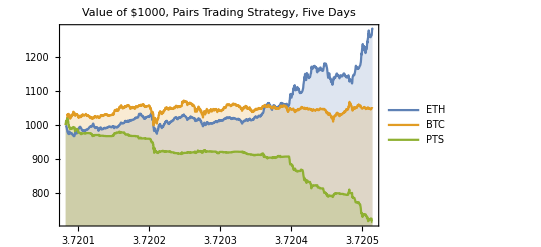

```mathematica
DateListPlot[{tsVETH,tsVBTC,tsVTD},Filling->Axis,PlotLabel->"Value of $1000, Pairs Trading Strategy, Five Days",
PlotLegends->{"ETH","BTC","PTS"}]
```

10 days back, was